```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,"/Users/mattmastin/Dropbox"];
```

```mathematica
<<knottheory`
```

Loading KnotTheory` version of March 22, 2011, 21:10:4.67737.
Read more at http://katlas.org/wiki/KnotTheory.

The following method will read symmetry input as mined from KnotInfo. A bit of pre-processing is needed. The symmetry types should be named:

full
reversible
positive
negative
chiral (no symmetry)

See the definitions below for the Whitten subgroups corresponding to each symmetry name.

In addition, knots should be end-line separated with whitespace seperating each knot name from the symmetry type.

```mathematica
ReadData[FileName_]:=Select[StringSplit[StringSplit[Import[FileName],"\n"]],Not[#=={}]&];
```

```mathematica
RawKnotData=ReadData["knotinfo-symmetryPD-blank.txt"];
```

Next we defnine the symmetry groups as lists of Whitten elements and define the corresponding replacement rules for either the groups or the cosets of each group in the Whitten group. Note that we are using the KnotInfo names for the symmetry groups.

```mathematica
full={{1,{1},{1}},{1,{-1},{1}},{-1,{1},{1}},{-1,{-1},{1}}};
reversible={{1,{1},{1}}{1,{-1},{1}}};
positive={{1,{1},{1}},{-1,{1},{1}}};
negative={{1,{1},{1}},{-1,{-1},{1}}};
chiral={{1,{1},{1}}};
```

These are just the replacement rules for getting the symmetry groups and cosets from the KnotInfo names.

```mathematica
SymReplacements={"full"->full,"reversible"->reversible,"positive"->positive,"negative"->negative,"chiral"->chiral };
```

```mathematica
CosetReplacements={"full"->{{1,{1},{1}}},"reversible"->{{1,{1},{1}},{-1,{1},{1}}},"positive"->{{1,{1},{1}},{1,{-1},{1}}},"negative"->{{1,{1},{1}},{1,{-1},{1}}},"chiral"->full};
```

```mathematica
RawKnotDataWithSyms=RawKnotData/.SymReplacements;
```

The entry for the PD codes are strings of the form “[[1,5,2,4],[3,1,4,6],[5,3,6,2]]” so we can just do some string manipulation to get the correct expression for use in KnotTheory.

```mathematica
GetPD[PDString_]:=ToExpression[StringInsert[StringInsert[StringReplace[StringDrop[StringDrop[PDString,1],-1],"["->"X["],"PD[",1],"]",-1]]
```

```mathematica
GetPD[RawKnotDataWithSyms[[1]][[3]]]
```

PD[X[1,5,2,4],X[3,1,4,6],X[5,3,6,2]]

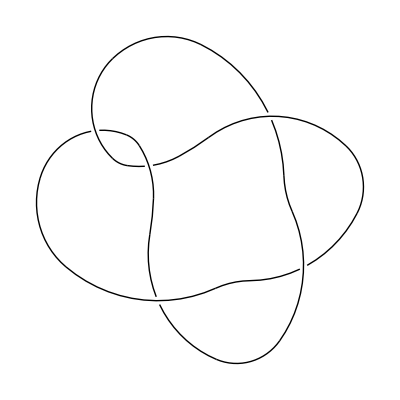

```mathematica
DrawPD[GetPD[RawKnotDataWithSyms[[4]][[3]]]]
```

```mathematica
RawKnotDataWithSyms[[1]][[3]]
```

[[1,5,2,4],[3,1,4,6],[5,3,6,2]]

Now we replace the PD codes with the correct expression and write the data to file.

```mathematica
KnotDataWithSyms=Table[ReplacePart[RawKnotDataWithSyms[[i]],3->GetPD[RawKnotDataWithSyms[[i]][[3]]]],{i,1,Length[RawKnotDataWithSyms]}];
```

```mathematica
Export["KnotDataWithSyms12.txt",KnotDataWithSyms];
```